```mathematica
SetDirectory[NotebookDirectory[]];
data=Partition[Delete[ReadList["data/outMexplicitEuler.txt", Real], 1], 2]
```

{{0.,1.},{-0.666667,0.866667},{-1.33333,0.6},{-1.91111,0.217778},{-2.31111,-0.244444},{-2.4563,-0.735704},{-2.29333,-1.19437},{-1.80286,-1.55494},{-1.00662,-1.75627}}

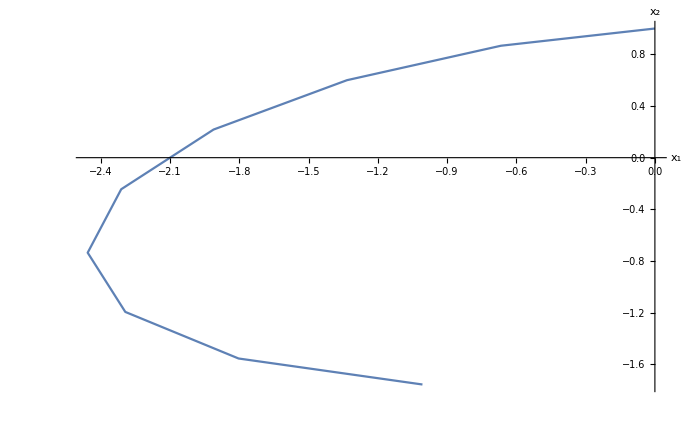

```mathematica
Show[ListLinePlot[{data},AxesLabel->{"x_1","x_2"},AxesStyle->Thick,LabelStyle->Directive[20]]]
```